```mathematica
x=Range[Pi,Pi+Pi/2,Pi/1000];
w=(Exp[I x]+I)/(Exp[I x]-I);
```

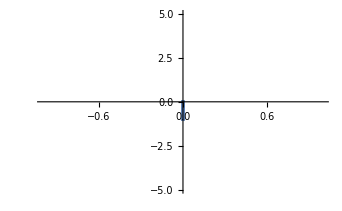

```mathematica
ListPlot[Transpose[{Re[w],Im[w]}],PlotRange->{{-1,1},{-5,5}}]
```

```mathematica
rgb={-1,N[Pi],4};

rgb={-1,2,2};
rgb={-1,4,5};
```

```mathematica
Graphics[{RGBColor[rgb/Norm[rgb]],ColorFunctionScaling->False,Disk[]},ImageSize->20]
```

-Graphics-

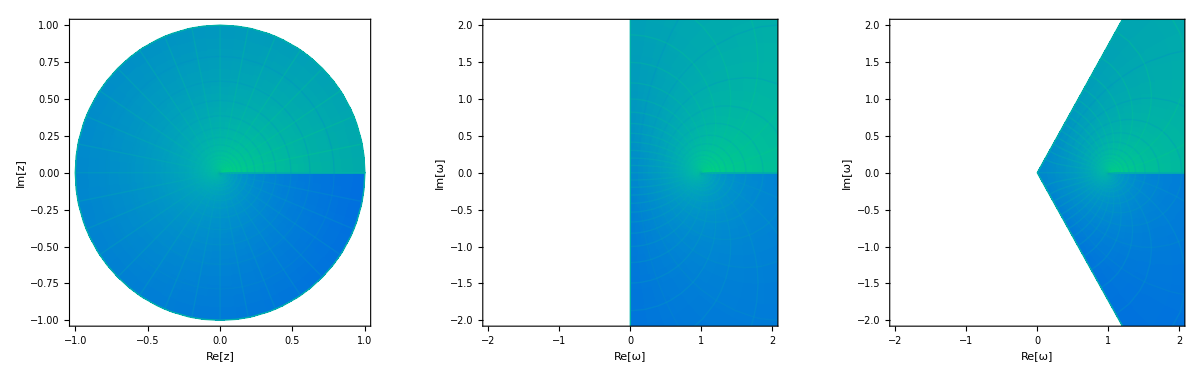

```mathematica
τmin=-5;τmax=0;σmin=0;σmax=2Pi;mesh1=20;mesh2=Round[5 2 Pi];con=1.;pr=2.;
redfun[τ_,σ_]:=-1
greenfun[τ_,σ_]:=-τ/2+2;
bluefun[τ_,σ_]:=(σ)/3+2;
rgbfun[τ_,σ_]:={redfun[τ,σ],greenfun[τ,σ],bluefun[τ,σ]}/Norm[{redfun[τ,σ],greenfun[τ,σ],bluefun[τ,σ]}];
f[τ_,σ_]:=((1+z)/(1-z))/.{z->Exp[τ+I σ]};
f2[τ_,σ_]:=((1+z)/(1-z))^(2/3)/.{z->Exp[τ+I σ]};

g1=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(z)/.{z->Exp[τ+I σ]}]],{τ,τmin,τmax},{σ,σmin,σmax},PlotRange->All,Axes->False,ImageSize->500,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},FrameLabel->{"Re[z]","Im[z]"}];

g2=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[f[τ,σ]]],{τ,τmin,τmax},{σ,σmin,σmax},Axes->False,ImageSize->490,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},PlotRange->{{-pr,pr},{-pr,pr}},FrameLabel->{"Re[ω]","Im[ω]"}];
g3=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[f2[τ,σ]]],{τ,τmin,τmax},{σ,σmin,σmax},Axes->False,ImageSize->490,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},PlotRange->{{-pr,pr},{-pr,pr}},FrameLabel->{"Re[ω]","Im[ω]"}];
fct=GraphicsRow[{g1,g2,g3}]
```

```mathematica
Export[NotebookDirectory[]<>"ct_close_re.jpg",fct,"JPG","CompressionLevel"->0]
```

C:\Users\sglil\OneDrive\Desktop\vertexState\code\draft\ct_close_re.jpg

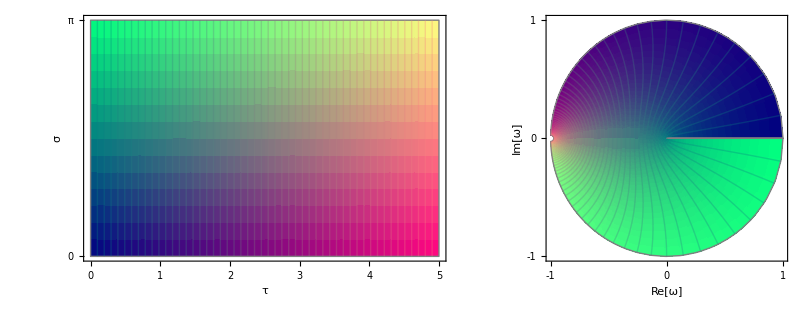

```mathematica
g1=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(ρ)/.{ρ->τ+I σ}]],{τ,0,5.},{σ,0, Pi},PlotRange->All,Axes->False,ImageSize->420,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{0,Pi},None},{{0,1,2,3,4,5},None}},FrameLabel->{
"τ","σ"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];

g2=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(I(1+I Exp[ρ])/(1-I Exp[ρ]))^2/.{ρ->τ+I σ}]],{τ,0.,5.},{σ,0, Pi},PlotRange->All,Axes->False,ImageSize->280,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},FrameLabel->{
"Re[ω]","Im[ω]"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];
GraphicsRow[{g1,g2}]
```

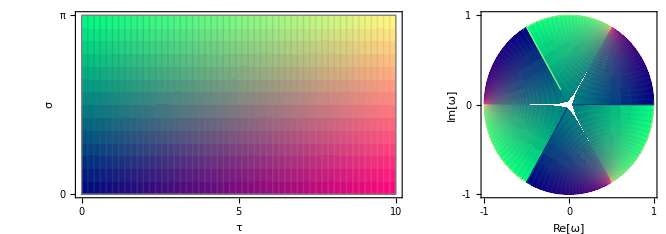

```mathematica
cf=-0.0005;z1=Exp[I Pi/6];z2=Exp[I 5Pi/6];z3=Exp[I Pi/2];
g1=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(ρ)/.{ρ->τ+I σ}]],{τ,0,10.},{σ,0+cf, Pi-cf},PlotRange->All,Axes->False,ImageSize->520,AspectRatio->0.5,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{0,Pi},None},{{0,5,10},None}},FrameLabel->{
"τ","σ"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];

g2=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(z1)^2((1+I Exp[ρ/2])/(1-I Exp[ρ/2]))^(2/3)/.{ρ->τ+I σ}]],{τ,0.,10.},{σ,0+cf, 2Pi-cf},PlotRange->All,Axes->False,ImageSize->280,AspectRatio->1,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},FrameLabel->{
"Re[ω]","Im[ω]"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];
g3=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(z2)^2((1+I Exp[ρ/2])/(1-I Exp[ρ/2]))^(2/3)/.{ρ->τ+I σ}]],{τ,0.,10.},{σ,0+cf,2 Pi-cf},PlotRange->All,Axes->False,ImageSize->280,AspectRatio->1,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},FrameLabel->{
"Re[ω]","Im[ω]"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];
g4=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(z3)^2((1+I Exp[ρ/2])/(1-I Exp[ρ/2]))^(2/3)/.{ρ->τ+I σ}]],{τ,0.,10.},{σ,0+cf,2 Pi-cf},PlotRange->All,Axes->False,ImageSize->280,AspectRatio->1,ColorFunction->Function[{x,y,τ,σ},RGBColor[τ,σ,0.5]],Mesh->{50,0},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},FrameLabel->{
"Re[ω]","Im[ω]"},LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}];
GraphicsRow[{g1,Show[{g2,g3,g4}]}]
```

```mathematica
τmin=-3;τmax=0;σmin=0;σmax=2Pi;(*inner unit circle*)
f[τ_,σ_]:=(-I(1-Exp[I Pi/3](z))/((z)-Exp[I Pi/3]))/.{z->Exp[τ+I σ]+1};
f[τ_,σ_]:=((z+I)/(z-I))/.{z->Exp[τ+I σ]+Exp[I Pi/6]};(*these two also give half plane*)

f[τ_,σ_]:=((1-I z)/(1+I z))^(2/3)/.{z->Exp[τ+I σ]} (*Witten*)
mesh1=16;mesh2=Round[8 2 Pi];con=2.;
rgbfun[τ_,σ_]:={τ+3,(σ)/2,con}/Norm[{τ+3,(σ)/2,con}];
(*τmin=-2;τmax=2;σmin=-Pi/2;σmax=Pi/2;
f[τ_,σ_]:=(-I(1-Exp[I Pi/3](z))/((z)-Exp[I Pi/3]))/.{z->Exp[τ+I σ]+1/2};*)
```

```mathematica
τmin=-3;τmax=0;σmin=0;σmax=2Pi;mesh1=16;mesh2=Round[8 2 Pi];con=2.;
rgbfun[τ_,σ_]:={τ+3,(σ)/2,con}/Norm[{τ+3,(σ)/2,con}];
f[τ_,σ_]:=((1+I z)/(1-I z))/.{z->Exp[τ+I σ]};
```

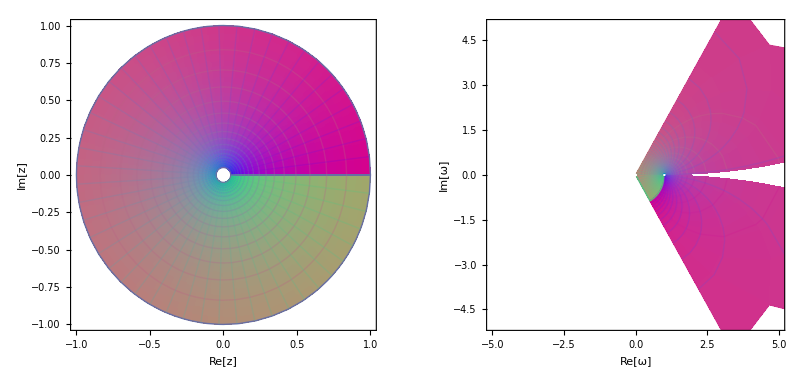

```mathematica
g1=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(z)/.{z->Exp[τ+I σ]}]],{τ,τmin,τmax},{σ,σmin,σmax},PlotRange->All,Axes->False,ImageSize->400,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},FrameLabel->{"Re[z]","Im[z]"}];

g2=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[f[τ,σ]]],{τ,τmin,τmax},{σ,σmin,σmax},Axes->False,ImageSize->390,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},PlotRange->{{-5,5},{-5,5}},FrameLabel->{"Re[ω]","Im[ω]"}];
GraphicsRow[{g1,g2}]
```

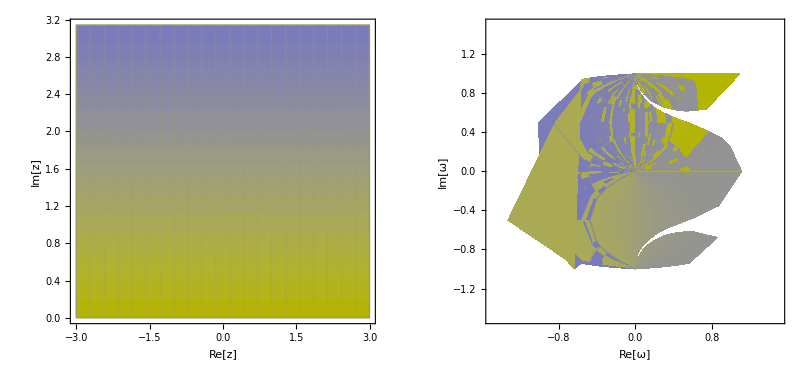

```mathematica
τmin=-3;τmax=3;σmin=0+0.00001;σmax=Pi-0.00001;
mesh1=20;mesh2=Round[5  Pi];
con=1.;pr=1.5;
redfun[τ_,σ_]:=1;
greenfun[τ_,σ_]:=1;
bluefun[τ_,σ_]:=(σ)/2;
rgbfun[τ_,σ_]:={redfun[τ,σ],greenfun[τ,σ],bluefun[τ,σ]}/Norm[{redfun[τ,σ],greenfun[τ,σ],bluefun[τ,σ]}];

f[τ_,σ_]:=1/π Log[(1+Exp[z Pi])/(1-Exp[z Pi])]/.{z->τ+I σ};

g00=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(Log[z])/.{z->Exp[τ+I σ]}]],{τ,τmin,τmax},{σ,σmin,σmax},PlotRange->All,Axes->False,ImageSize->500,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},FrameLabel->{"Re[z]","Im[z]"}];

g0=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[(Log[z])/.{z->Exp[τ+I σ]}]],{τ,τmin,τmax},{σ,σmin,σmax},PlotRange->All,Axes->False,ImageSize->500,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},FrameLabel->{"Re[z]","Im[z]"}];

g=ParametricPlot[Evaluate@Simplify@ComplexExpand@Through[{Re,Im}[f[τ,σ]]],{τ,τmin,τmax},{σ,σmin,σmax},Axes->False,ImageSize->490,ColorFunction->Function[{x,y,τ,σ},RGBColor[rgbfun[τ,σ]]],ColorFunctionScaling->False,Mesh->{mesh1,mesh2},PlotRange->{{-pr,pr},{-pr,pr}},FrameLabel->{"Re[ω]","Im[ω]"}];

fct=GraphicsRow[{g00,g}]
```

```mathematica
f[0.000001,0]
```

4.25387+1. ⅈ